```mathematica
V[r_]=V0*E^(-r^2/a^2);
```

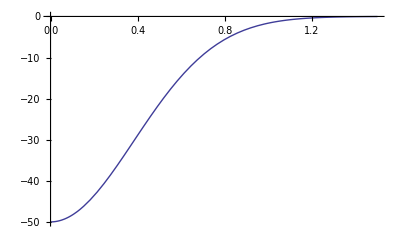

```mathematica
Plot[V[r],{r,0,1.5}]
```

```mathematica
d=Integrate[E^(-(b^2+z^2)/x),{z,-Infinity,Infinity}]
```

If[Re[x]>0,ⅇ^(-b^2/x) √π √x,Integrate[ⅇ^(-(b^2+z^2)/x),{z,-∞,∞},Assumptions→Re[x]≤0]]